1.4845

-0.63

-1.758

1.4215

-0.518

1.2

10

1.2 (0.46944 √x-0.063 x-0.01758 x^2+0.0014215 x^3-0.0000518 x^4)

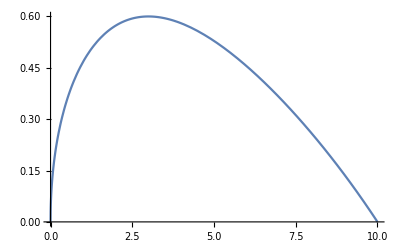

{0.,0.322772,0.544174,0.592421,0.420066,-1.33227×10^-16}

```mathematica
aux=x/fCord;
a0=1.4845
a1=-0.6300
a2=-1.7580
a3=1.4215

a4=-0.518
fTT=1.2
fCord=10
val=fTT*(a0*Sqrt[aux]+a1*aux+a2*aux*aux+a3*aux*aux*aux+a4*aux*aux*aux*aux)
Plot[val,{x,0,10}]
Table[val/.x->t^2 /10,{t,0,10,2}]
```